# Pipeline Algebra

## Embeddings + Classification

Translate the quantum circuit operations into purely matrix/vector-based operations (i.e., classical linear algebra). 💃
Represent Qubits and Registers as Vector Spaces
- Each qubit is a 2D complex vector space with computational basis ∣0⟩ = (1
0) and ∣1⟩ = (0
1).
- An 𝑛-qubit register corresponds to a tensor product space of dimension 2^𝑛.
- A full quantum state is a normalized vector in this space.
- Initialize the nodes in an equal superposition, not with different .

# Network Parameters (real)

```mathematica
SetDirectory["C:\\Users\\mpatr\\Documents\\Thesis\\ThesisWork"];
edgesRaw = Import["dataset/OmniPath_gene_edges_filtered_with_index.csv"];
degreesRaw = Import["dataset/OmniPath_gene_degrees_filtered_with_index.csv"];
featuresRaw = Import["dataset/MutSig_gene_pvalues_filtered_with_index.csv"];
```

```mathematica
edgesHeader = edgesRaw[[1]];
colIndex1 = FirstPosition[edgesHeader, "index1"][[1]];
colIndex2 = FirstPosition[edgesHeader, "index2"][[1]];

degreesHeader = degreesRaw[[1]];
colDegIndex = FirstPosition[degreesHeader, "index"][[1]];
colDegree = FirstPosition[degreesHeader, "Degree"][[1]];

featuresHeader = featuresRaw[[1]];
colFeatIndex = FirstPosition[featuresHeader, "index"][[1]];
colMutsig = FirstPosition[featuresHeader, "mutsig_score"][[1]];

(* Edges, Degrees \*)
edges = Map[ToExpression, edgesRaw[[2 ;; , {colIndex1, colIndex2}]], {2}];
degreeAssoc = AssociationThread[
  ToExpression[degreesRaw[[2 ;; , colDegIndex]]] -> 
  ToExpression[degreesRaw[[2 ;; , colDegree]]]
];
nrNodes = Length[degreeAssoc];
Print["Number of nodes: ", nrNodes];
(* --- Features vector aligned to node indices --- *)
features = Table[featureAssoc[i], {i, 1, nrNodes}];
featureAssoc = AssociationThread[
  ToExpression[featuresRaw[[2 ;; , colFeatIndex]]] -> 
  ToExpression[featuresRaw[[2 ;; , colMutsig]]]
];

(* --- Adjacency list: each edge is added in both directions --- *)
adjacencyList = Table[{}, {nrNodes}];
Scan[
  (adjacencyList[[#[[1]]]] = Append[adjacencyList[[#[[1]]]], #[[2]]];
   adjacencyList[[#[[2]]]] = Append[adjacencyList[[#[[2]]]], #[[1]]]) &,
  edges
];

nodeDegreesC1 = AssociationMap[
  Total[degreeAssoc /@ adjacencyList[#]] &,
  Keys[degreeAssoc]
];

(* --- Compute m_c1 and s_c1 --- *)
maxD = Max[Values[degreeAssoc]]; m = Ceiling[Log2[maxD]]; s = 2^m;
Print["Immediate neighbors: max=", maxD, ", m=", m, ", s=", s];
maxC1 = Max[Values[nodeDegreesC1]]; mC1 = Ceiling[Log2[maxC1]]; sC1 = 2^mC1;
Print["Second-hop neighbors: max=", maxC1, ", m_c1=", mC1, ", s_c1=", sC1];
```

Number of nodes: 6850

Immediate neighbors: max=601, m=10, s=1024

```mathematica
(*--------------------------------------- Check Results ---------------------------------------*)

(* --- Edges --- *)
Print["Edges (first 10):"];
Print[edges[[1 ;; 10]]];

(* --- Adjacency list --- *)
Print["AdjacencyList (first 10 nodes):"];
Do[
  Print["Node ", i, " neighbors: ", adjacencyList[[i]]],
  {i, 1, Min[10, nrNodes]}
];

(* --- Number of Neighbors --- *)
Print["DegreeAssoc (first 10):"];
Print[Take[degreeAssoc, 10]];
Print["NodeDegreesC1 (first 10 nodes):"];
Print[nodeDegreesC1[[1 ;; 10]]];
(* --- Features association --- *)
Print["FeatureAssoc (first 10):"];
Print[Take[featureAssoc, 10]];
```

Edges (first 10):

{{670,6402},{672,6402},{671,6402},{729,6402},{1620,6402},{3547,6402},{2981,6402},{3488,6402},{2461,6402},{5896,6402}}

AdjacencyList (first 10 nodes):

Node 1 neighbors: {1271}

Node 2 neighbors: {1356,3646,3654,3335}

Node 3 neighbors: {4087,241,244,5908,946,956,2477,3465,3476,4739}

Node 4 neighbors: {4729,3718,3717,4738,5283}

Node 5 neighbors: {3481,1066,421}

Node 6 neighbors: {5910,962,2181}

Node 7 neighbors: {5744,266,3569,4729,1746,4566,279,5135,3284,1946,5522,1324,4739,4752,5283}

Node 8 neighbors: {266}

Node 9 neighbors: {6275,2147,2146,4738,4729,5283}

Node 10 neighbors: {946,2477,3476}

DegreeAssoc (first 10):

<|2477→601,946→521,4738→482,3470→455,956→442,4729→435,3465→400,5827→368,6513→338,5283→330|>

NodeDegreesC1 (first 10 nodes):

{{1,1},{2,96},{3,2558},{4,1313},{5,361},{6,184},{7,1751},{8,14},{9,1667},{10,1411}}

FeatureAssoc (first 10):

<|6275→15.9546,4463→15.9546,4837→15.9546,3169→15.9546,253→15.9546,4467→15.9546,573→15.9546,973→15.9546,2011→15.9546,4037→15.9546|>

```mathematica
(*--------------------------------------- Dimensions for each register ---------------------------------------*)

swapDim = 2^5 * 2^3 * 2^m * 2^m;
fullDim = swapDim * 2^p * 2^mC1 * 2^n * 2^n * 2^n; (* dim-features * dim_Z * dim_K * dim_u1 * dim_U2 * dim_V *)

(* number of qubits: QuantumCircuit(qr_a, qr_z, qr_k, qr_u2, qr_u1, qr_l2, qr_l1, qr_c, qr_i, qr_v) *)
Print["Full dimension: ", fullDim];
Print["Swap dimension: ", swapDim];
Print["Full dim (qubits): ", Log2[fullDim]]
Print["Swap dim (qubits): ", Log2[swapDim]]
```

Full dimension: 2^(8+2 m+3 n+p+Ceiling[Log[Missing[KeyAbsent,1]^2]/Log[2]])

Swap dimension: 2^(8+2 m)

Full dim (qubits): Log[2^(8+2 m+3 n+p+Ceiling[Log[Missing[KeyAbsent,1]^2]/Log[2]])]/Log[2]

Swap dim (qubits): Log[2^(8+2 m)]/Log[2]

# Unitary Gates

## Simple Gates

```mathematica
H = (1/Sqrt[2]) * {
  {1, 1},
  {1, -1}
};

H2 = (1/2) * {
  {1, 1, 1, 1},
  {1, -1, 1, -1},
  {1, 1, -1, -1},
  {1, -1, -1, 1}
};

H3 = (1/Sqrt[8]) * {
  {1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1}
};

H4 = (1/4) * {
  {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1},
  {1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1, 1, -1},
  {1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1},
  {1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1, 1, -1, -1, 1},
  {1, 1, 1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1},
  {1, -1, 1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1},
  {1, 1, -1, -1, -1, -1, 1, 1, 1, 1, -1, -1, -1, -1, 1, 1},
  {1, -1, -1, 1, -1, 1, 1, -1, 1, -1, -1, 1, -1, 1, 1, -1},
  {1, 1, 1, 1, 1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1},
  {1, -1, 1, -1, 1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1},
  {1, 1, -1, -1, 1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1},
  {1, -1, -1, 1, 1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1},
  {1, 1, 1, 1, -1, -1, -1, -1, -1, -1, -1, -1, 1, 1, 1, 1},
  {1, -1, 1, -1, -1, 1, -1, 1, -1, 1, -1, 1, 1, -1, 1, -1},
  {1, 1, -1, -1, -1, -1, 1, 1, -1, -1, 1, 1, 1, 1, -1, -1},
  {1, -1, -1, 1, -1, 1, 1, -1, -1, 1, 1, -1, 1, -1, -1, 1}
};
```

```mathematica
(*--------------------------------------- Hadamard Matrices ---------------------------------------*)

Hl = Switch[m,
  1, H,
  2, H2,
  3, H3,
  4, H4,
  _, MessageDialog["Only m = 1 to 4 supported"]
];

(*--------------------------------------- Feature Rotation Matrix ---------------------------------------*)

Wtheta[theta_] := {
  {Cos[theta/2], -Sin[theta/2]},
  {Sin[theta/2],  Cos[theta/2]}
};

Wval[val_] := {
  {val, -Sqrt[1 - val^2]},
  {Sqrt[1 - val^2], val}
};

Print["Wtheta[0.5] =", MatrixForm[Wtheta[0.5]]];
Print["Wval[1] =", MatrixForm[Wval[0.8]]];
```

Wtheta[0.5] =(0.968912 | -0.247404
0.247404 | 0.968912)

Wval[1] =(0.8 | -0.6
0.6 | 0.8)

## OL: Equivalent Feature Rotation

Given node v and neighbor index l, it retrieves the 2x2 feature rotation matrix F_X(u=r(v,l)) to act on the 1-qubit ancilla .

```mathematica
Print["Creating FeatureRotation gate..."]
GetFeatureRotation[v_Integer, l_Integer] := Module[
  {u, featVal},

  (* Check if v and l are valid indices *)
  If[
    1 <= v <= Length[adjacencyList] && 1 <= l <= Length[adjacencyList[[v]]],
    
    u = adjacencyList[[v, l]]; (* In Mathematica, indexing starts at 1 *)
    featVal = features[[u]];
    Wval[featVal],
    (* Return identity if invalid *)
    IdentityMatrix[2]
  ]
];

MatrixForm[GetFeatureRotation[1, 1]]
MatrixForm[GetFeatureRotation[2, 1]]
MatrixForm[GetFeatureRotation[2, 2]]
Print["Finished."]
```

Creating FeatureRotation gate...

(1 | 0
0 | 1)

(1 | 0
0 | 1)

(1 | 0
0 | 1)

Finished.

## OK^-1: Equivalent Feature Rotation

Given node v and neighborhood-hop index c, it retrieves the 2x2 feature rotation matrix F_K(v) to act on the 1-qubit ancilla .

```mathematica
Print["Creating DegreeRotation gate..."]
GetDegreeRotation[v_Integer, c_Integer] := Module[
  {deg, theta},
  
  deg = Switch[c,
    1, nodeDegrees[[v]],
    2, nodeDegreesC1[[v]],
    _, Return[IdentityMatrix[2]] 
  ];

  If[deg < 1, Return[IdentityMatrix[2]]];
  theta = 2 ArcCos[1 / deg];
  Wtheta[theta]
];

MatrixForm[GetDegreeRotation[2, 1]]
MatrixForm[GetDegreeRotation[2, 2]]
Print["Finished."]
```

Creating DegreeRotation gate...

Part::partd: Part specification nodeDegrees⟦2⟧ is longer than depth of object.

(1/nodeDegrees⟦2⟧ | -√(1-1/nodeDegrees⟦2⟧^2)
√(1-1/nodeDegrees⟦2⟧^2) | 1/nodeDegrees⟦2⟧)

Part::partw: Part 2 of {Missing[KeyAbsent,1]^2} does not exist.

(1/({Missing[KeyAbsent,1]^2}⟦2⟧) | -√(1-1/(({Missing[KeyAbsent,1]^2}⟦2⟧)^2))
√(1-1/(({Missing[KeyAbsent,1]^2}⟦2⟧)^2)) | 1/({Missing[KeyAbsent,1]^2}⟦2⟧))

Finished.

# QMME Circuit

## c=1: Feature Embeddings for (v, l, i)

First-hop neighborhood: For each (v, l), get the 8 feature vectors (for each i, l) of dimension  = 16 (corresponding to 4 ancilla rotations).

```mathematica
Print["Creating firstHopStates..."];

firstHopStates = Reap[
  Do[
    featVec = GetFeatureRotation[v, l] . {1, 0};
    
    (* Precompute all Kronecker combinations once for each featVec *)
    vectListBase = Table[{1, 0}, {4}];
    
    Do[
      vectList = ReplacePart[vectListBase, Table[k -> featVec, {k, 1, i}]];
      combinedVec = Fold[KroneckerProduct, First[vectList], Rest[vectList]] // Flatten;
      
      Sow[<|
        "v" -> v,
        "i" -> i,
        "l" -> l,
        "u" -> adjacencyList[[v, l]],
        "featVec" -> featVec,
        "state" -> combinedVec
      |>],
      {i, 1, 4}
    ],
    {v, 1, nrNodes}, {l, 1, s}
  ]
][[2, 1]];

(* firstHopStates // TableForm *)
(* Select[firstHopStates, #v == 2 &] // TableForm *)
(* Scan[Print[Norm[#state]] &, firstHopStates] *) (* Norm = 1 for all *)
Print["Finished."]
```

Creating firstHopStates...

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Finished.

## c=2: Feature Embeddings for (v, l1, l2, i) - Taking a while for real-sized Net

Second-hop neighborhood: For each (v, l1, l2), get the 16 feature vectors (for each i, l1, l2) of dimension  = 16 (corresponding to 4 ancilla rotations).

```mathematica
(* Preprocess: group firstHopStates by "v" *)
firstHopByV = GroupBy[firstHopStates, #["v"] &];

Print["Creating secondHopStates..."];
secondHopStates = Reap[
  For[v0 = 1, v0 <= nrNodes, v0++,
    For[l0 = 1, l0 <= s, l0++,
      u0 = adjacencyList[[v0, l0]];
      neighborStates = Lookup[firstHopByV, u0, {}];  (* fast! *)

      Do[
        Sow[<|
          "v" -> v0,
          "i" -> state["i"],
          "l0" -> l0,
          "u0" -> u0,
          "l1" -> state["l"],
          "u1" -> state["u"],
          "state" -> state["state"]
        |>],
        {state, neighborStates}
      ];
    ]
  ]
][[2, 1]];

(* secondHopStates // TableForm *)
(* Select[secondHopStates, #v == 3 &] // TableForm *)
(* Scan[Print[Norm[#state]] &, secondHopStates] *) (* Norm = 1 for all *)
Print["Finished."]
```

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Creating secondHopStates...

Part::partw: Part 1 of {} does not exist.

Finished.

## Superposition from firstHopsStates

First-hop neighborhood: For each (v, i), get the one feature vectors of dimension  = 64 (corresponding to 5 ancilla rotations and the l register).

```mathematica
groupedByVI = GroupBy[firstHopStates, {#v, #i} &];

Print["Creating firstHopSuperposedStates..."]
firstHopSuperposedStates = KeyValueMap[
  Function[{key, states},
    Module[{c = 1, v, i, stateDim = 16, combinedState, HOnL, hadState, finalState, degRotVec},
      {v, i} = key;
      
      combinedState = Flatten[states[[All, "state"]]];  (* length = s * 16 *)

      HOnL = KroneckerProduct[Hl, IdentityMatrix[stateDim]];  (* 16s x 16s matrix *)
      hadState = HOnL . combinedState / Sqrt[s];

      degRotVec = GetDegreeRotation[v, c] . {1, 0};  (* length 2 vector *)
      finalState = Flatten[KroneckerProduct[hadState, degRotVec]];

      <|
        "c" -> c,
        "v" -> v,
        "i" -> i,
        "stateCombined" -> combinedState,
        "stateHadamardL" -> hadState,
        "degRotVec" -> degRotVec,
        "stateDegreeRotated" -> finalState
      |>
    ]
  ],
  groupedByVI
];

(* Select[firstHopSuperposedStates, #v == 2 && #i == 4 &] *)
(* Scan[Print[Norm[#stateDegreeRotated]] &, firstHopSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
```

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Creating firstHopSuperposedStates...

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[{Do[featVec=GetFeatureRotation[«2»].{«2»};vectListBase=Table[{«2»},{«1»}];Do[Set[«2»];Set[«2»];Sow[«1»],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&] is not a valid Association.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[{Do[featVec=GetFeatureRotation[«2»].{«2»};vectListBase=Table[{«2»},{«1»}];Do[Set[«2»];Set[«2»];Sow[«1»],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&] is not a valid Association.

Finished.

## Superposition from secondHopsStates

Second-hop neighborhood: For each (v, i), get the one feature vectors of dimension  = 128 (corresponding to 5 ancilla rotations and the l registers).

```mathematica
groupedByVI2 = GroupBy[secondHopStates, {#v, #i} &];

Print["Creating secondHopSuperposedStates..."]
secondHopSuperposedStates = KeyValueMap[
  Function[{key, states},
    Module[{c = 2, v, i, stateDim = 16, combinedState, HOnL, hadState, finalState, degRotVec},
      {v, i} = key;
      
      combinedState = Flatten[states[[All, "state"]]];  

      HOnL = KroneckerProduct[Hl, Hl, IdentityMatrix[stateDim]];  (* 16s^2 x 16s^2 matrix *)
      hadState = HOnL . combinedState / s;

      degRotVec = GetDegreeRotation[v, c] . {1, 0}; 
      finalState = Flatten[KroneckerProduct[hadState, degRotVec]]; (* 2 x as big as for c = 1 *)

      <|
        "c" -> c,
        "v" -> v,
        "i" -> i,
        "stateCombined" -> combinedState,
        "stateHadamardL" -> hadState,
        "degRotVec" -> degRotVec,
        "stateDegreeRotated" -> finalState
      |>
    ]
  ],
  groupedByVI2
];

(* Select[secondHopSuperposedStates, #v == 2 && #i == 4 &] *)
(* Scan[Print[Norm[#stateDegreeRotated]] &, secondHopSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
```

GroupBy::list1: The argument {Null,{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Creating secondHopSuperposedStates...

KeyValueMap::invak: The argument GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&] is not a valid Association.

Finished.

## Feature Embeddings f_x(v,c,i)

Both neighborhoods: For each (v, c, i), get the one feature vectors of dimension  = 128 (padded and unit-length).

```mathematica
Print["Creating allSuperposedStates..."]
allSuperposedStates = Join[
  (* c = 1: pad to 2^5 * s^2 = 2^(5+2m) *)
  Map[
    Function[assoc,
      assoc ~Join~ <|
        "statePadded" -> PadRight[assoc["stateDegreeRotated"], 2^5 * s^2]
      |>
    ],
    firstHopSuperposedStates
  ],

  (* c = 2: already full size *)
  Map[
    Function[assoc,
      assoc ~Join~ <|
        "statePadded" -> assoc["stateDegreeRotated"]
      |>
    ],
    secondHopSuperposedStates
  ]
];

Map[
  Function[assoc,
    <|
      "c" -> assoc["c"],
      "i" -> assoc["i"],
      "stateLengthPadded" -> Length[assoc["statePadded"]]
    |>
  ],
  Select[allSuperposedStates, #v == 2 &]
]

(* Scan[Print[Norm[#statePadded]] &, allSuperposedStates]*) (* Norm = 1 for all *)
Print["Finished."]
```

Creating allSuperposedStates...

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[{Do[featVec=GetFeatureRotation[«2»].{«2»};vectListBase=Table[{«2»},{«1»}];Do[Set[«2»];Set[«2»];Sow[«1»],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&] is not a valid Association.

Function::fpct: Too many parameters in {key,states} to be filled from Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√s);degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]][stateDegreeRotated].

PadRight::ilsm: List of machine-sized integers expected at position 2 in PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]][stateDegreeRotated],32 s^2].

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,«13»,HOnL,hadState,finalState,degRotVec},«1»]][…],«1»]|>] cannot be joined.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

PadRight::ilsm: List of machine-sized integers expected at position 2 in PadRight[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2].

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

PadRight::ilsm: List of machine-sized integers expected at position 2 in PadRight[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2].

General::stop: Further output of PadRight::ilsm will be suppressed during this calculation.

Join::incpt: Incompatible elements in Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] cannot be joined.

KeyValueMap::invak: The argument Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] is not a valid Association.

KeyValueMap::invak: The argument GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&] is not a valid Association.

General::stop: Further output of KeyValueMap::invak will be suppressed during this calculation.

Function::fpct: Too many parameters in {key,states} to be filled from Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]][stateDegreeRotated].

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][s…ed]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

GroupBy::argx: GroupBy called with 2 arguments; 1 argument is expected.

General::stop: Further output of GroupBy::argx will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,«13»,HOnL,hadState,finalState,degRotVec},«1»]][…],«1»]|>] cannot be joined.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Join::incpt: Incompatible elements in Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] cannot be joined.

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][s…ed]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

Function::slot1: (#v==2&)[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[Part[«3»]];HOnL=KroneckerProduct[Hl,IdentityMatrix[«1»]];hadState=Dot[«2»] Power[«2»];degRotVec=GetDegreeRotation[«2»].{«2»};finalState=Flatten[KroneckerProduct[«2»]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][stateDegreeRotated],32 s^2]|>]] is expected to have an Association as the first argument.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Function::slot1: (#v==2&)[Join[GroupBy[{Do[Set[«2»];Set[«2»];Do[«2»],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>]] is expected to have an Association as the first argument.

Function::slot1: (#v==2&)[Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[Part[«3»]];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[«1»]];hadState=Dot[«2»] Power[«2»];degRotVec=GetDegreeRotation[«2»].{«2»};finalState=Flatten[KroneckerProduct[«2»]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][stateDegreeRotated]|>]] is expected to have an Association as the first argument.

General::stop: Further output of Function::slot1 will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 0 arguments; 1 or 2 arguments are expected.

KeyValueMap[]

Finished.

## Feature Embeddings f_x(v)

Both neighborhoods: For each , get the one feature vectors of dimension  = 128x8=1024 (unit-length).

```mathematica
(* Group all states by v *)
vectorsByV = GroupBy[allSuperposedStates, #v &];

(* For each v, build the concatenated super-long vector by joining statePadded vectors in order *)
Print["Creating superLongVectorsByV..."]
superLongVectorsByV = Association[
  KeyValueMap[
    Function[{v, assocList},
      lookup = Association[Map[{#c, #i} -> # &, assocList]];
      
      concatenatedVector = Flatten[
        Table[
          If[KeyExistsQ[lookup, {c, i}],
            lookup[{c, i}]["statePadded"] / Sqrt[8],  (* superposition in (c,i) *)
            {}
          ],
          {c, 1, 2}, {i, 1, 4}
        ],
        Infinity
      ];
      
      v -> concatenatedVector
    ],
    vectorsByV
  ]
];

(* Norm /@ Values[superLongVectorsByV] // Print Norm = 1 for all *)
(* Print[Dimensions /@ Values[superLongVectorsByV]] *)
Print["Finished."]
```

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,«13»,HOnL,hadState,finalState,degRotVec},«1»]][…],«1»]|>] cannot be joined.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Join::incpt: Incompatible elements in Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] cannot be joined.

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][s…ed]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

GroupBy::list1: The argument KeyValueMap[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[Part[«3»]];HOnL=KroneckerProduct[Hl,IdentityMatrix[«1»]];hadState=Dot[«2»] Power[«2»];degRotVec=GetDegreeRotation[«2»].{«2»};finalState=Flatten[KroneckerProduct[«2»]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][sta…ated],«1»]|>],«2»,«1»] is not a valid list of Associations or rules or lists of rules.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

Creating superLongVectorsByV...

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,«13»,HOnL,hadState,finalState,degRotVec},«1»]][…],«1»]|>] cannot be joined.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Join::incpt: Incompatible elements in Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] cannot be joined.

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][s…ed]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

GroupBy::list1: The argument KeyValueMap[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[Part[«3»]];HOnL=KroneckerProduct[Hl,IdentityMatrix[«1»]];hadState=Dot[«2»] Power[«2»];degRotVec=GetDegreeRotation[«2»].{«2»};finalState=Flatten[KroneckerProduct[«2»]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][sta…ated],«1»]|>],«2»,«1»] is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[KeyValueMap[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{«2»}=key;combinedState=Flatten[«1»];HOnL=KroneckerProduct[«2»];hadState=Times[«2»];degRotVec=Dot[«2»];finalState=Flatten[«1»];Association[Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][stateDegreeRotated],32 s^2]|>],«1»,«1»,Join[GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&],<|statePadded→GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&][stateD…Rotated]|>]],«1»] is not a valid Association.

Finished.

# Swap-Test Classifier

Expectation value of the product of two Pauli-Z operators acting on the ancilla qubits of the quantum classifier’s state.
It measures their correlation and captures the similarity between the test data and training data.

## Kernel Matrix on Training Data

Values::invrl: The argument Association[KeyValueMap[Function[{v,assocList},lookup=Association[(«1»&)/@assocList];concatenatedVector=Flatten[Table[If[«3»],{«3»},{«3»}],∞];v→concatenatedVector],vectorsByV]] is not a valid Association or a list of rules.

Creating Kernel Matrix Table...

{1,1}

Creating Kernel Matrix Heatmap...

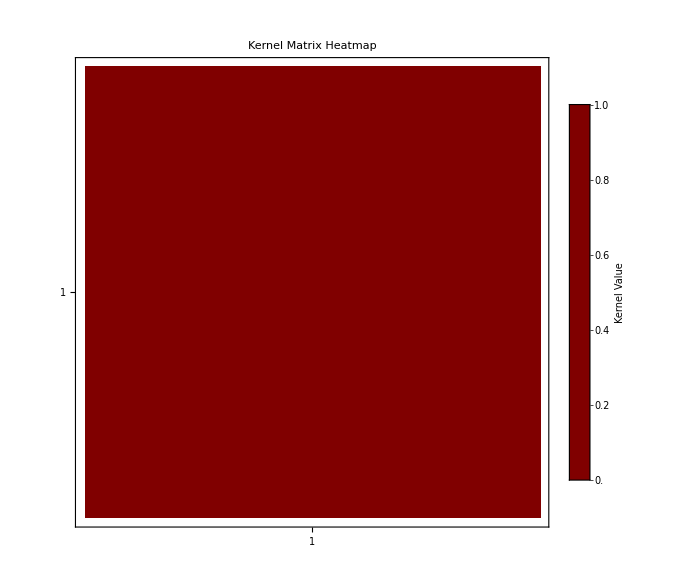

```mathematica
trainVecs = Values[superLongVectorsByV];
nPower = 1;

Print["Creating Kernel Matrix Table..."]
kernelMatrix = Table[
  (Abs[trainVecs[[i]] . trainVecs[[j]]])^(2 nPower),
  {i, Length[trainVecs]}, {j, Length[trainVecs]}
];

Dimensions[kernelMatrix] (* should be {nrNodes, nrNodes} *)

Print["Creating Kernel Matrix Heatmap..."]
Legended[
 MatrixPlot[kernelMatrix,
  ColorFunction -> "TemperatureMap",
  FrameTicks -> True,
  PlotLabel -> "Kernel Matrix Heatmap",
  ImageSize -> Large
 ],
 BarLegend[{"TemperatureMap", {Min[kernelMatrix], Max[kernelMatrix]}}, LegendLabel -> "Kernel Value"]
]
```

## Classification

```mathematica
(* Train/Test Set Details *)
thClass = 0.5;
classLabels = If[# < thClass, 0, 1] & /@ features;

wV = ConstantArray[1/nrNodes, nrNodes];
(* wV = {1/2, 1/6, 1/6, 1/6}; *)

Print["Class labels: ", classLabels];
(* Print["Features: ", features]; *)

testNode = 1; (* 1 in Mathematica. 0 in Python. *)
```

Class labels: {If[Missing[KeyAbsent,1]<0.5,0,1]}

```mathematica
trainLabels = classLabels; (* {1, 1, 0, 0}; *)
testIsTrain = True

Print["Calculating Expectation Values..."]
expectationValsAll = If[testIsTrain,
  Table[
    Total[((-1)^trainLabels) * wV * kernelMatrix[[v]]],
    {v, Length[trainVecs]}
  ],
  
  (* if testIstrain = False, exclude self from kernel row, labels and weights *)
  Table[
    Module[{idxs = Delete[Range[Length[trainVecs]], v]},
      Total[
        ((-1)^trainLabels[[idxs]]) * wV[[idxs]] * kernelMatrix[[v, idxs]]
      ]
    ],
    {v, Length[trainVecs]}
  ]
];

Print["Calculating Predicted Labels..."]
predictedLabels = 1/2 (1 - Sign[expectationValsAll]);

results = Table[
  <|
    "Node" -> v,
    "ExpectationValue" -> expectationValsAll[[v]],
    "TrueLabel" -> trainLabels[[v]],
    "PredictedLabel" -> predictedLabels[[v]],
    "Correct" -> (predictedLabels[[v]] == trainLabels[[v]])
  |>,
  {v, Length[trainVecs]}
];

(* Print /@ results; *)
```

True

Calculating Expectation Values...

Calculating Predicted Labels...

Creating Results Bar Chart...

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/(√(«1»));degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,«13»,HOnL,hadState,finalState,degRotVec},«1»]][…],«1»]|>] cannot be joined.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

Join::incpt: Incompatible elements in Join[GroupBy[{Do[featVec=Dot[«2»];vectListBase=Table[«2»];Do[CompoundExpression[«3»],{«3»}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&],<|statePadded→PadRight[GroupBy[{Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[vectListBase,Table[k→featVec,{k,1,i}]];combinedVec=Flatten[Fold[KroneckerProduct,First[vectList],Rest[vectList]]];Sow[Association[v→v,i→i,l→l,u→adjacencyList⟦v,l⟧,featVec→featVec,state→combinedVec]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧,{#v,#i}&][stateDegreeRotated],32 s^2]|>] cannot be joined.

Join::incpt: Incompatible elements in Join[Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[states⟦All,state⟧];HOnL=KroneckerProduct[Hl,Hl,IdentityMatrix[stateDim]];hadState=(HOnL.combinedState)/s;degRotVec=GetDegreeRotation[v,c].{1,0};finalState=Flatten[KroneckerProduct[hadState,degRotVec]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→Function[{key,states},Module[{c=2,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][s…ed]|>] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

GroupBy::list1: The argument KeyValueMap[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{v,i}=key;combinedState=Flatten[Part[«3»]];HOnL=KroneckerProduct[Hl,IdentityMatrix[«1»]];hadState=Dot[«2»] Power[«2»];degRotVec=GetDegreeRotation[«2»].{«2»};finalState=Flatten[KroneckerProduct[«2»]];Association[c→c,v→v,i→i,stateCombined→combinedState,stateHadamardL→hadState,degRotVec→degRotVec,stateDegreeRotated→finalState]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][sta…ated],«1»]|>],«2»,«1»] is not a valid list of Associations or rules or lists of rules.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

Part::partw: Part 1 of {} does not exist.

GroupBy::list1: The argument {Do[featVec=GetFeatureRotation[v,l].{1,0};vectListBase=Table[{1,0},{4}];Do[vectList=ReplacePart[«2»];combinedVec=Flatten[«1»];Sow[Association[«6»]],{i,1,4}],{v,1,nrNodes},{l,1,s}],{}}⟦2,1⟧ is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

Do::iterb: Iterator {l,1,s} does not have appropriate bounds.

General::stop: Further output of Do::iterb will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

KeyValueMap::argt: KeyValueMap called with 4 arguments; 1 or 2 arguments are expected.

General::stop: Further output of KeyValueMap::argt will be suppressed during this calculation.

BarChart::chsty: Value of option ChartStyle -> {If[1/2 (1-Sign[Power[«2»]] Sign[«1»]^2)==If[Missing[KeyAbsent,1]<0.5,0,1],Green,Red]} is not a style or group of styles.

KeyValueMap::invak: The argument GroupBy[KeyValueMap[Join[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},{«2»}=key;combinedState=Flatten[«1»];HOnL=KroneckerProduct[«2»];hadState=Times[«2»];degRotVec=Dot[«2»];finalState=Flatten[«1»];Association[Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]]]],<|statePadded→PadRight[Function[{key,states},Module[{c=1,v,i,stateDim=16,combinedState,HOnL,hadState,finalState,degRotVec},«1»]][stateDegreeRotated],32 s^2]|>],«1»,«1»,Join[GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&],<|statePadded→GroupBy[{Null,{}}⟦2,1⟧,{#v,#i}&][stateD…Rotated]|>]],«1»] is not a valid Association.

General::stop: Further output of KeyValueMap::invak will be suppressed during this calculation.

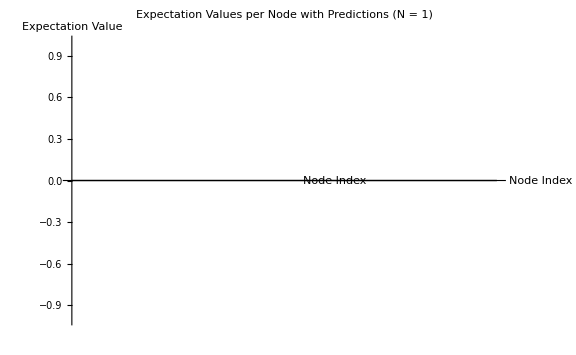

```mathematica
showLabels = True;  (* or True *)

Print["Creating Results Bar Chart..."]
BarChart[
  expectationValsAll,
  ChartStyle -> (If[#["Correct"], Green, Red] & /@ results),
  ChartLabels -> If[
    showLabels,
    Placed[
      Map[
        Row[{
          Style["True: " <> ToString[#["TrueLabel"]], Bold],
          "\n",
          Style["Predicted: " <> ToString[#["PredictedLabel"]], Italic]
        }] &,
        results
      ],
      Below
    ],
    None
  ],
  PlotLabel -> StringForm["Expectation Values per Node with Predictions (N = ``)", nrNodes],
  AxesLabel -> {"Node Index", "Expectation Value"},
  ImageSize -> Large
]
```

```mathematica
(* Compute metrics *)
trueLabels = results[[All, "TrueLabel"]];
predLabels = results[[All, "PredictedLabel"]];
posClass = 1; negClass = 0;

(* True Positives: predicted = 1 AND true = 1 *)
tp = Count[results, assoc_ /; assoc["PredictedLabel"] == posClass && assoc["TrueLabel"] == posClass];
(* False Positives: predicted = 1 AND true = 0 *)
fp = Count[results, assoc_ /; assoc["PredictedLabel"] == posClass && assoc["TrueLabel"] == negClass];
(* False Negatives: predicted = 0 AND true = 1 *)
fn = Count[results, assoc_ /; assoc["PredictedLabel"] == negClass && assoc["TrueLabel"] == posClass];

accuracy = N[Count[results[[All, "Correct"]], True]/Length[results]]; (* correct / all *)
precision = If[tp + fp == 0, 0, N[tp/(tp + fp)]]; (*tp / all predicted positives*)
recall = If[tp + fn == 0, 0, N[tp/(tp + fn)]]; (* tp / all real positives *)
f1 = If[precision + recall == 0, 0, 2*precision*recall/(precision + recall)];

(* Metrics table *)
metricsTable = Grid[
  {{"Metric", "Value"},
   {"Accuracy", accuracy},
   {"Precision", precision},
   {"Recall", recall},
   {"F1 Score", f1}},
  Frame -> All
];

metricsTable
```

Metric | Value
Accuracy | 0.
Precision | 0
Recall | 0
F1 Score | 0